# Frequency vs Time Delay

```mathematica
(*Preliminaries*)
rootDir = ParentDirectory[NotebookDirectory[]];
rowDir =FileNameJoin[{rootDir, "ResultPictures1","RowGrids"}];
spectrumFitsDir=FileNameJoin[{rootDir, "ResultPictures1","SpectrumFits"}];
SetDirectory[FileNameJoin[{rootDir,"Data", "FreqDelay"}]];
pulsarName = "B0329+54_w1";

 
(*Select region of data*)
regionSelect[data_,x1_,x2_] := Select[data,x1<#[[1]]<x2 && #[[2]]>0&];
(*Full Width Half Maximum*)
half[data_]:=Nearest[Table[data[[i,2]]->i,{i,Length[data]}],0.5*Max[data[[All,2]]],1];
FWHM[data_,half_]:=First[Abs[(data[[half,1]]-data[[First[Position[data[[All,2]],Max[data[[All,2]]]]],1]])*2]];
```

```mathematica
(*Importing data*)
raw = Import[pulsarName <> "_raw.txt", "Table"];
time = Flatten[Import [pulsarName <>"_time.txt", "Table"]];
freq = Flatten[Import[pulsarName <> "_freq.txt", "Table"]];
data = ParallelTable[Transpose[{time,raw[[i]]}],{i,1,Length@raw}];
```

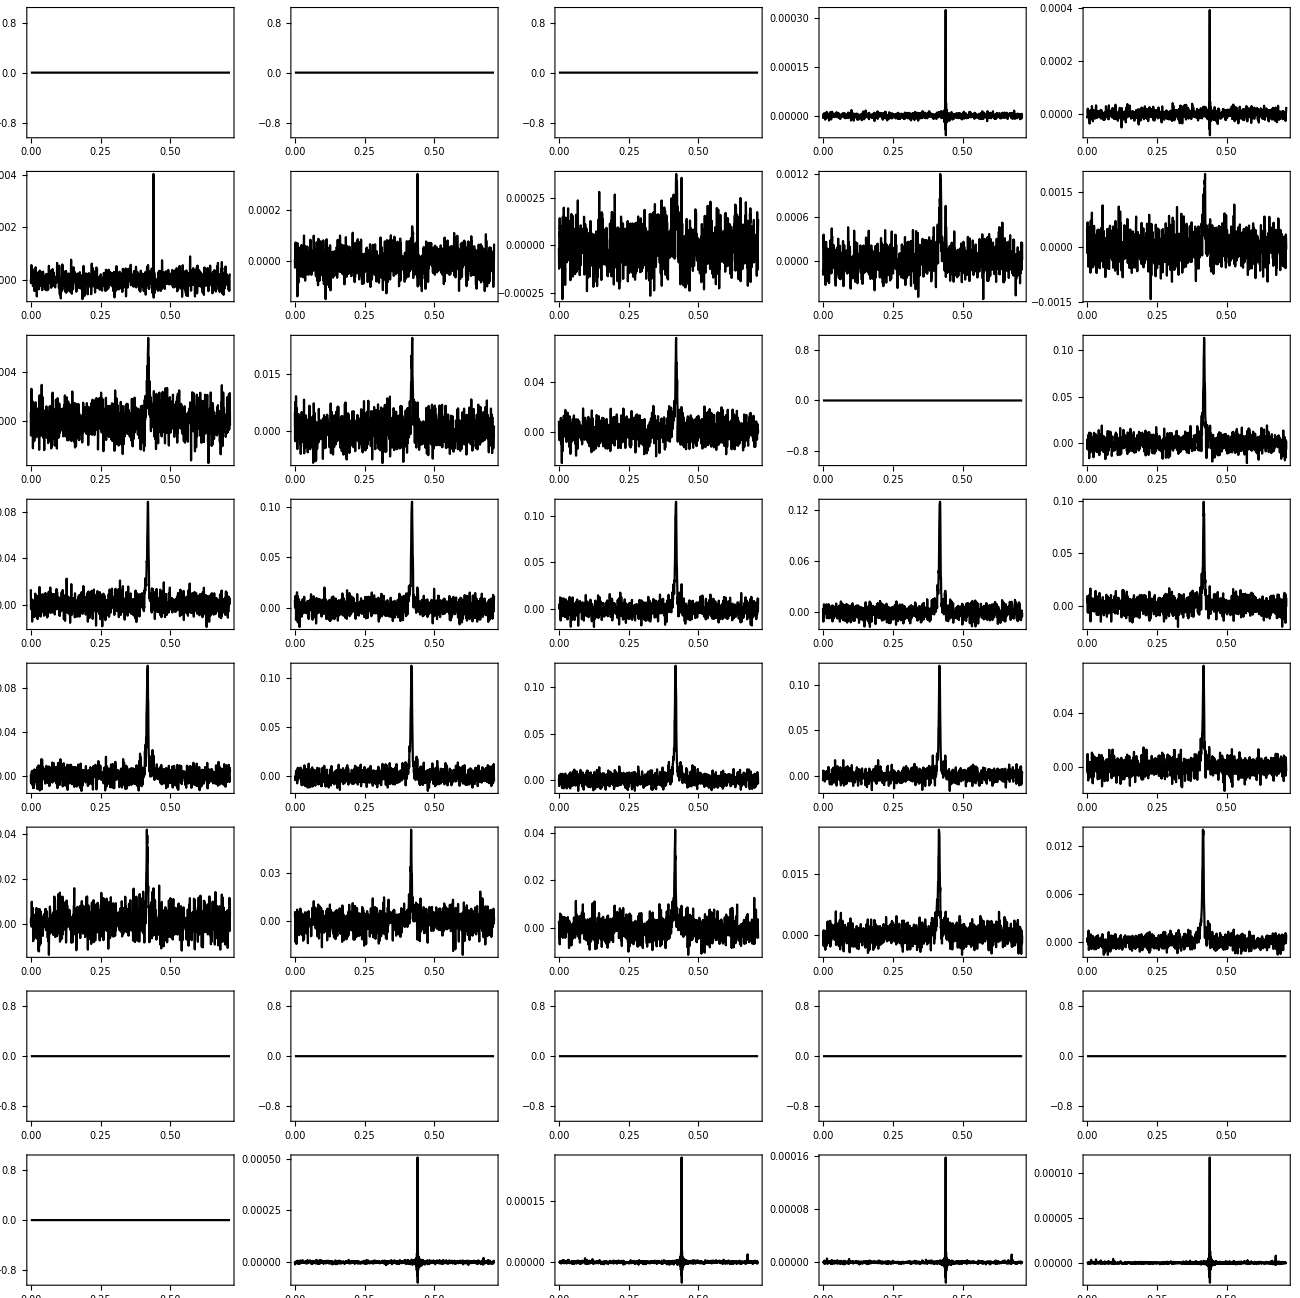

/home/patrick/CrabPulsar/materials/ResultPictures1/RowGrids/B0329+54_w1.png

```mathematica
(*Table of Raw Plots*)
plots = ParallelTable[ListLinePlot[data[[i]],PlotStyle->Black,Frame->True,PlotRange->All, ImageSize->500],{i,1,Length@data}];
plots = Partition[plots,5];
grid = GraphicsGrid[plots,ImageSize->1300, PlotLabel->pulsarName <> "\n", LabelStyle->Directive[25,Bold]]
Export[FileNameJoin[{rowDir,pulsarName <> ".png"}],grid]
```

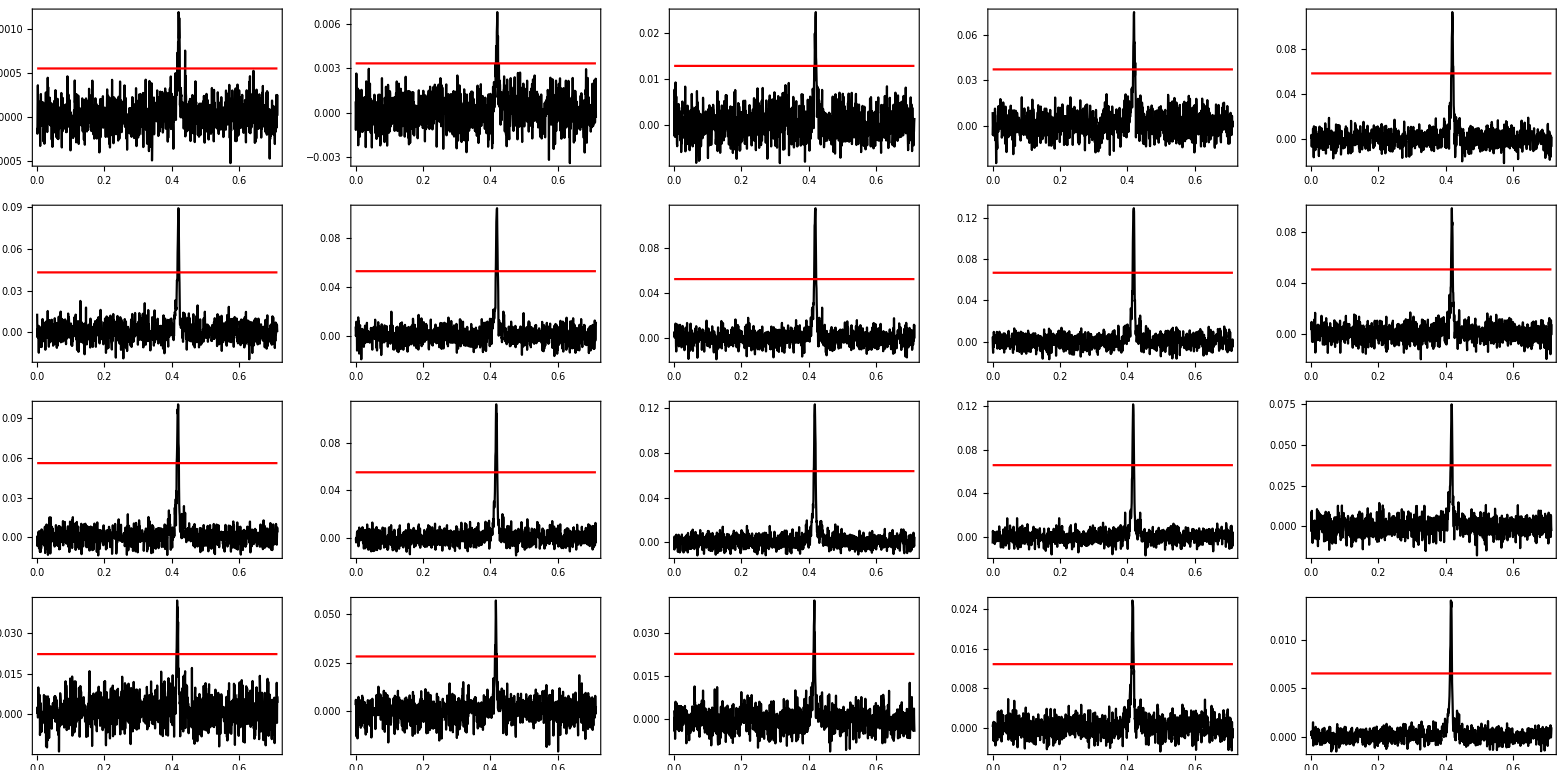

```mathematica
(*Eliminate bad data*)
filtData = data[[9;;30]];
filtData = Delete[filtData,6];
filtData = Delete[filtData,2];

(*Find where the FWHM is and its value*)
halfsPos = ParallelTable[half[filtData[[i]]],{i,1,Length@filtData}];
halfs = ParallelTable[filtData[[i]][[All,2]][[half[filtData[[i]]][[1]]]],{i,1,Length@filtData}];
fwhms = ParallelTable[FWHM[filtData[[i]],halfsPos[[i]]],{i,1,Length@halfsPos}];

(*Create Table of plots indicating this*)
filtPlots = ParallelTable[Show[ListLinePlot[filtData[[i]],PlotStyle->Black,Frame->True,PlotRange->All, ImageSize->500],Plot[halfs[[i]],{x,Min[data[[i]][[All,1]]],Max[data[[i]][[All,1]]]},PlotStyle->Red]],{i,1,Length@filtData}];
filtPlots = Partition[filtPlots,5];
GraphicsGrid[filtPlots,ImageSize->1700, PlotLabel->"Filtered Data - FWHF Position Indicated", LabelStyle->Directive[25,Bold]]
```

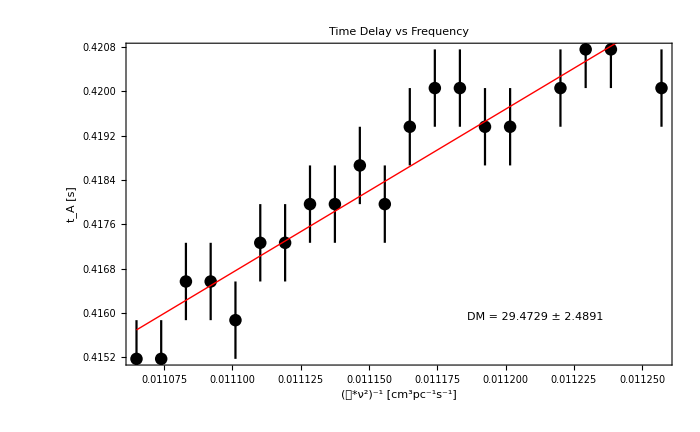

/home/patrick/CrabPulsar/materials/ResultPictures1/SpectrumFits/B0329+54_w1.png

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.089582 | 0.0277631 | 3.22666 | 0.00467983
x | 29.4729 | 2.4891 | 11.8408 | 6.25504×10^-10

```mathematica
Needs["ErrorBarPlots`"]
(*Find maximum peaks in the filtered data*)
maxs = ParallelTable[Max[filtData[[i]][[All,2]]],{i,1,Length@filtData}];
maxsPos = ParallelTable[Position[filtData[[i]][[All,2]],maxs[[i]]][[1]][[1]],{i,1,Length@filtData}];


(*Get the time data*)
times = time[[maxsPos]];
σtimes = Abs[time[[maxsPos+1]] - time[[maxsPos-1]]]/2;

(*Get the frequency data*)
freqs = freq[[9;;30]];
freqs = Delete[freqs,6];
freqs = Delete[freqs,2];
xdata = 10^4/(2.410*freqs^2) ;

(*Fitting*)
fitData = Transpose[{xdata,times}];
lm = LinearModelFit[fitData,x,x, Weights->1/σtimes^2];
plotData = Table[{fitData[[i]],ErrorBar[σtimes[[i]]]},{i,Length@fitData}];

(*The plot*)
Show[ErrorListPlot[plotData,PlotStyle->{Black},PlotRange->All],Plot[lm[x],{x,Min[xdata],Max[xdata]},PlotStyle->{Red,Thick},PlotRange->All],Frame->True,ImageSize->700, PlotLabel->"Time Delay vs Frequency",FrameLabel->{"(𝒟*ν^2)^-1 [cm^3pc^-1s^-1]","t_A [s]"},LabelStyle->Directive[20],FrameStyle->Directive[20,Black], Epilog->{ Inset[Framed[Text[Style["DM = " <> ToString@lm["BestFitParameters"][[2]] <> " ± " <>ToString@lm["ParameterErrors"][[2]],FontFamily->Times, FontSize->20]], RoundingRadius->2], Scaled[{0.75,0.15}]]}]

Export[FileNameJoin[{spectrumFitsDir,pulsarName <> ".png"}],%]
lm["ParameterTable"]
```